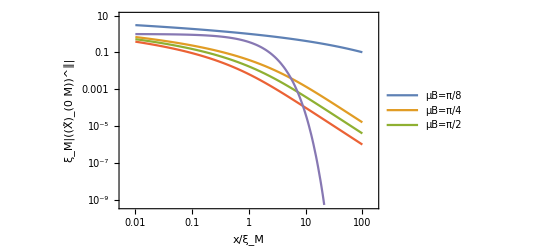

```mathematica
(*Shrinking of cloud due to magnetic field*)
g[Δ_,ϕ_,x_]:= Abs[Exp[(Δ+I ϕ)x]Gamma[0,(Δ +I ϕ)x]/(2π)]^2
p1=LogLogPlot[{g[1/1000,0,x],g[1/1000,π/8,x],g[1/1000,π/4,x],g[1/1000,π/2,x],Exp[-x]},{x,0.01,100},BaseStyle->{FontSize->14,FontFamily->"Helvetica"},Frame->True,Axes->False,FrameLabel->{"x/ξ_M","ξ_M|((X̃)_(0  M))^∥|"},PlotLegends->Placed[{"μB=π/8","μB=π/4","μB=π/2"},{Left,Bottom}]];
Show[p1]
```

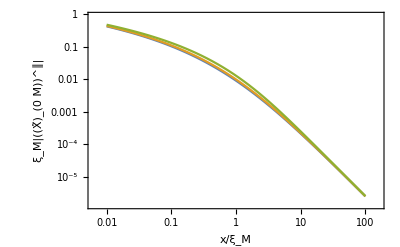

```mathematica
f[ϕ_,x_]:= Abs[Exp[Exp[I ϕ] x]Gamma[0,Exp[I ϕ] x]/(2π)]^2
p2=LogLogPlot[{f[0,x],f[π/4,x],f[π/2,x]},{x,0.01,100},BaseStyle->{FontSize->14,FontFamily->"Helvetica"},Frame->True,Axes->False,FrameLabel->{"x/ξ_M","ξ_M|((X̃)_(0  M))^∥|"},PlotRange->All];
Show[p2]
```